```mathematica
datastring=Import[NotebookDirectory[]<>"opvalues.txt"];
```

```mathematica
header = ImportString[datastring,"Table"][[1;;2]];data=Drop[ImportString[datastring,"Table"],2];
```

```mathematica
header
```

{{#,L=,20,beta=,[0.25],t_max=,4.,steps=,100,D=,[15]},{t,E,mag}}

```mathematica
t = data[[All,1]];
energy = data[[All,2]];
mag = data[[All,3]];
```

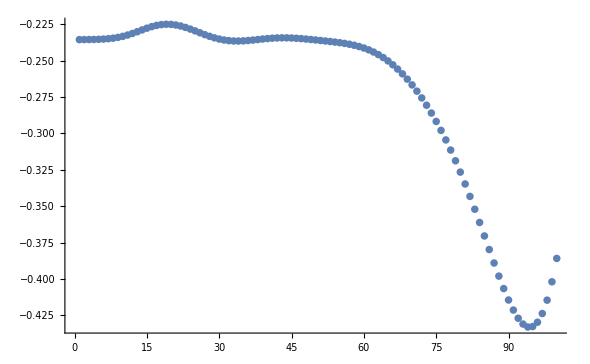

```mathematica
ListPlot[mag]
```